# Fourier Series and Transform

According to Eqs. (4.1) and (4.2), in the text, we can express a square integrable function f(x) as a sum of trigonometric functions so that

-Graphics-

in the interval -L/2 < x < L/2, where

-Graphics-

Let’s take an interval of length  L=1 and the triangle function

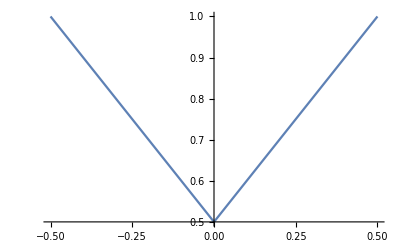

```mathematica
ClearAll["Global`*"]
L=1;
f[x_]:=Abs[-x]+L/2 
Plot[f[x],{x,-L/2,L/2}]
```

We numerically calculate the Fourier coefficients a_n, b_n

```mathematica
a0:=1/L NIntegrate[f[x],{x,-L/2,L/2}]
a[n_]:=2/L NIntegrate[f[x] Cos[2π n x/L],{x,-L/2,L/2},AccuracyGoal->5]
b[n_]:=2/L NIntegrate[f[x] Sin[2π n x/L],{x,-L/2,L/2}]
```

and store them in array up to some arbitrary maximum value max=100;

```mathematica
max=100;
a0
acoffs=Table[Chop[a[n]],{n,1,max}]
bcoffs=Table[b[n],{n,1,max}]
```

0.75

{-0.202642,0,-0.0225158,0,-0.00810569,0,-0.00413556,0,-0.00250176,0,-0.00167473,0,-0.00119907,0,-0.000900633,0,-0.000701185,0,-0.000561336,0,-0.000459507,0,-0.000383067,0,-0.000324228,0,-0.000277973,0,-0.000240954,0,-0.000210866,0,-0.000186081,0,-0.000165422,0,-0.000148022,0,-0.00013323,0,-0.000120549,0,-0.000109596,0,-0.00010007,0,-0.0000917349,0,-0.0000843992,0,-0.0000779094,0,-0.0000721404,0,-0.0000669892,0,-0.0000623707,0,-0.0000582138,0,-0.0000544591,0,-0.0000510563,0,-0.0000479627,0,-0.000045142,0,-0.000042563,0,-0.0000401988,0,-0.0000380263,0,-0.0000360253,0,-0.0000341782,0,-0.0000324695,0,-0.0000308859,0,-0.0000294154,0,-0.0000280474,0,-0.0000267727,0,-0.0000255829,0,-0.0000244708,0,-0.0000234296,0,-0.0000224534,0,-0.0000215371,0,-0.0000206757,0}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

Note: because of the symmetry of f(x) in the interval, all b_n coefficients vanish and the  a_n for n>0, vanish for even n. Thus

```mathematica
Ff[x_,num_]:=a0+Sum[acoffs[[n]] Cos[2 Pi n x/L],{n,1,num}]
```

Let’s look at a partial series for the partial sum indices num=1,5,11 respectively

0.75-0.202642 Cos[2 π x]

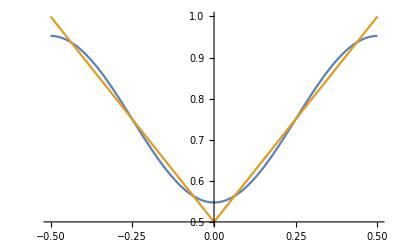

```mathematica
Ff[x,1]
Plot[{%,f[x]},{x,-L/2,L/2}]
```

0.75-0.202642 Cos[2 π x]-0.0225158 Cos[6 π x]-0.00810569 Cos[10 π x]

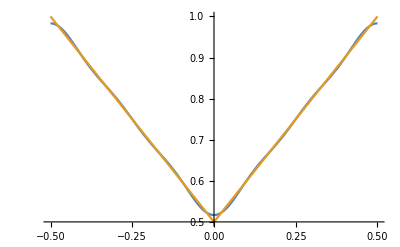

```mathematica
Ff[x,5]
Plot[{%,f[x]},{x,-L/2,L/2}]
```

0.75-0.202642 Cos[2 π x]-0.0225158 Cos[6 π x]-0.00810569 Cos[10 π x]-0.00413556 Cos[14 π x]-0.00250176 Cos[18 π x]-0.00167473 Cos[22 π x]

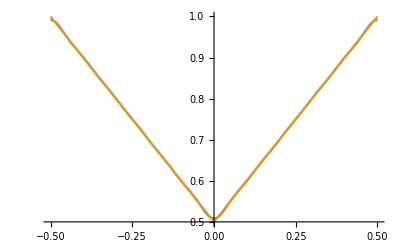

```mathematica
Ff[x,11]
Plot[{%,f[x]},{x,-L/2,L/2}]
```

Notice that the Fourier sum approximates the function f(x) ever more accurately as we increase the partial sum index.

### Problems

For the above interval construct the Fourier sum for the function

f(x)= x.

(1) As you increase the value of the partial sum index, how does the Fourier sum compare with f(x)  in the region near the endpoints of the interval, i.e.  at x=±1/2? 

(2) Construct the quantity 

S_n≡∫_(-L/2)^(L/2)| fourier_n(x) - f(x) |^2 dx

where fourier_n(x) is the nth partial Fourier sum for f(x).  Explore the behavior S_nas the index n→ ∞.  Compare that with your observations in (1).  The oscillatory behavior  of the Fourier sum, at the endpoints,  persist  as n→ ∞, is called the Gibbs phenomenon.

```mathematica
URL["https://en.wikipedia.org/wiki/Gibbs_phenomenon"]
```

URL[https://en.wikipedia.org/wiki/Gibbs_phenomenon]

## Fourier Transform

In the limit as L→∞, the Fourier series of a function melds into the Fourier transform pair, Eq. (4.5)

-Graphics-
The function h(ξ) is called the Fourier transform of function f(x), and vice-versa.

```mathematica
?FourierTransform
```

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr. 
FourierTransform[expr,{t_1,t_2,…},{ω_1,ω_2,…}] gives the multidimensional Fourier transform of expr.

Note: The internal Mathematica function for the Fourier Transform is defined somewhat differently from that given in  Eq. (4.5). See the above entry for the alternative, Mathematica, definition.

Suppose we wish to express the function f(x)=sin[x] Exp[-x^2] as a Fourier integral

```mathematica
fun[x_]=Sin[x]Exp[-x^2]
h[u_]=FullSimplify[FourierTransform[Sin[x] Exp[-x^2],x,u]]
```

ⅇ^(-x^2) Sin[x]

(ⅈ ⅇ^(-1/4 (1+u)^2) (-1+ⅇ^u))/(2 √2)

To check whether the above integrand does indeed represent f(x) when inserted into the integral we construct the following table

```mathematica
ftable[x_]:=Chop[NIntegrate[ h[u]/Sqrt[2 Pi]Exp[-I u x],{u,-∞,∞},AccuracyGoal->9]]
```

```mathematica
table1=Table[{x,fun[x]},{x,-2,2,0.1}];
table2=Table[{x,ftable[x]},{x,-2,2,0.1}];
```

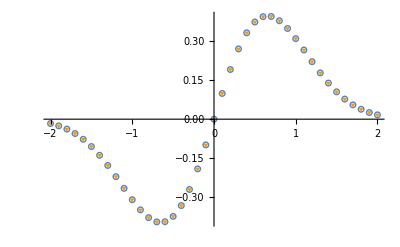

```mathematica
ListPlot[{table1,Re[table2]},PlotMarkers->{{○,Large},{▼,Large}}]
```

In the figure above the empty circles represent data from the original function f(x), whereas the triangle represent data obtained numerically with its Fourier transform.